84350294911456044599486768675168

0.002721799176662840767971275107961158196589829049142715205338737954425747185714900371862252507645305382666669706086166531875010074739055376662342618656731265705116159068739943951160240904751505289034954

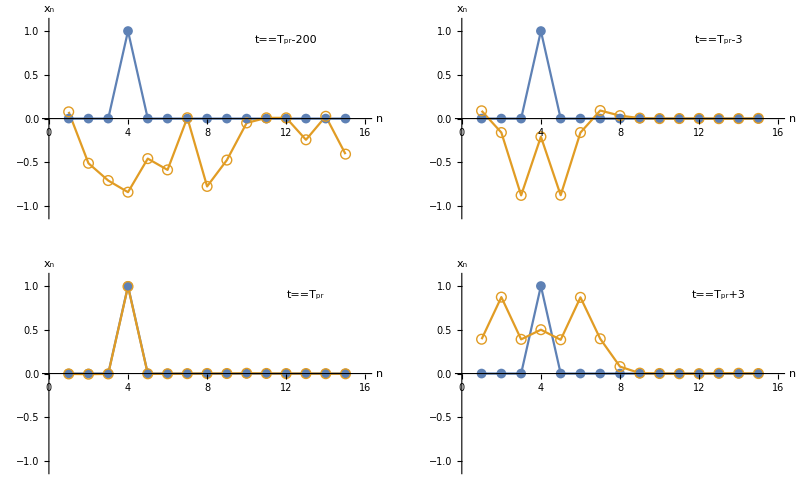

```mathematica
(*Poincare recurrence of a harmonic chain*)
num = 15;
nulist = 2 * Sin[Range[num]*Pi/2/(num+1)];
alpha =Take[nulist,{1,num-1}]/nulist[[num]];
ind1 =4;
ind2 = ind1 ;
x0p0 = Table[0,{i,1, num},{j,1,2}];
x1p1 =x0p0;
x0p0[[ind1, 1]]=1;
x0p0[[ind2,2]]= 1;
basis = Sqrt[2/(num+1)]*Table[Sin[i*j*Pi/(num+1)],{i,1,num},{j,1,num}];
proj0 = basis.x0p0;
projtr = Table[0,{i,1,num},{j, 1,2}];
projp1 = Table[0,{i,1,num},{j, 1,2}];
projm1 = Table[0,{i,1,num},{j, 1,2}];
proj13 = Table[0,{i,1,num},{j, 1,2}];
Q = 10^35;
A = Table[0,{i, 1,  num},{j,1,num}];
A[[1, 1]] = 1; 
For[i=1, i ≤num-1, i++, A[[1, i+1]]=Round[Q*alpha[[i]]];];
For[i=2, i≤num, i++, A[[i,i]] = Q; ];
bb = LatticeReduce[A];
q = Abs[bb[[1,1]]]
error = Abs[N[q*alpha - Round[q* alpha],200]];
Max[error]
rectime= N[q*2*Pi/(nulist[[num]]), 200] ;
time = rectime;
For[i=1, i≤num, i++, projtr[[i]]= {Cos[time*nulist[[i]]]*proj0[[i,1]]+Sin[time*nulist[[i]]]*proj0[[i,2]]/nulist[[i]],-Sin[time*nulist[[i]]]*nulist[[i]]*proj0[[i,1]]+Cos[time*nulist[[i]]]*proj0[[i,2]]};];
time = rectime +3;
For[i=1, i≤num, i++, projp1[[i]]= {Cos[time*nulist[[i]]]*proj0[[i,1]]+Sin[time*nulist[[i]]]*proj0[[i,2]]/nulist[[i]],-Sin[time*nulist[[i]]]*nulist[[i]]*proj0[[i,1]]+Cos[time*nulist[[i]]]*proj0[[i,2]]};];
time = rectime -3;
For[i=1, i≤num, i++, projm1[[i]]= {Cos[time*nulist[[i]]]*proj0[[i,1]]+Sin[time*nulist[[i]]]*proj0[[i,2]]/nulist[[i]],-Sin[time*nulist[[i]]]*nulist[[i]]*proj0[[i,1]]+Cos[time*nulist[[i]]]*proj0[[i,2]]};];
time =  rectime  -200;
For[i=1, i≤num, i++, proj13[[i]]= {Cos[time*nulist[[i]]]*proj0[[i,1]]+Sin[time*nulist[[i]]]*proj0[[i,2]]/nulist[[i]],-Sin[time*nulist[[i]]]*nulist[[i]]*proj0[[i,1]]+Cos[time*nulist[[i]]]*proj0[[i,2]]};];
xptr= basis.projtr;
xpp1 = basis.projp1;
xpm1 = basis.projm1;
xp13 = basis.proj13;
fontxy = 12;
t11 = ListLinePlot[{x0p0[[All,1]],xp13[[All, 1]]} ,AxesLabel -> {"n",Style[Subscript["x","n"]]},   TicksStyle->Small,AxesStyle-> fontxy, PlotRange->{{0, 16}, {-1.1, 1.1}}, PlotMarkers->{{"●",10}, {"○",10}}];
t12 = Graphics[Text[t==Subscript[T,pr] -200,{12,0.9}]];
t1 = Show[t11,t12];
t21 = ListLinePlot[{x0p0[[All,1]],xpm1[[All, 1]]} ,AxesLabel -> {"n",Style[Subscript["x","n"]]},   TicksStyle->Small,AxesStyle->fontxy, PlotRange->{{0, 16}, {-1.1, 1.1}}, PlotMarkers->{{"●",10}, {"○",10}}];
t22 = Graphics[Text[t==Subscript[T,pr]-3,{13,0.9}]];
t2 = Show[t21,t22];
t31 = ListLinePlot[{x0p0[[All,1]],xptr[[All, 1]]} ,AxesLabel -> {"n",Style[Subscript["x","n"]]},   TicksStyle->Small,AxesStyle->fontxy, PlotRange->{{0, 16}, {-1.1, 1.1}}, PlotMarkers->{{"●",10}, {"○",10}}];
t32 = Graphics[Text[t==Subscript[T,pr],{13,0.9}]];
t3= Show[t31,t32];
t41= ListLinePlot[{x0p0[[All,1]],xpp1[[All, 1]]} ,AxesLabel -> {"n",Style[Subscript["x","n"]]},   TicksStyle->Small,AxesStyle->fontxy, PlotRange->{{0, 16}, {-1.1, 1.1}}, PlotMarkers->{{"●",10}, {"○",10}}];
t42 = Graphics[Text[t==Subscript[T,pr]+3,{13,0.9}]];
t4= Show[t41,t42];
fig1 = Show[GraphicsGrid[{{t1, t2},{t3,t4}}]]
t11 = ListLinePlot[{x0p0[[All,2]],xp13[[All, 2]]} ,AxesLabel -> {"n",Style[Subscript["p","n"]]},   TicksStyle-> Small,AxesStyle->fontxy, PlotRange->{{0, 16}, {-1.1, 1.1}}, PlotMarkers->{{"●",10}, {"○",10}}];
t12 = Graphics[Text[t==Subscript[T,pr] -200,{12,0.9}]];
t1 = Show[t11,t12];
t21 = ListLinePlot[{x0p0[[All,2]],xpm1[[All, 2]]} ,AxesLabel -> {"n",Style[Subscript["p","n"]]},   TicksStyle->Small,AxesStyle->fontxy, PlotRange->{{0, 16}, {-1.1, 1.1}}, PlotMarkers->{{"●",10}, {"○",10}}];
t22 = Graphics[Text[t==Subscript[T,pr]-3,{13,0.9}]];
t2 = Show[t21,t22];
t31 = ListLinePlot[{x0p0[[All,2]],xptr[[All, 2]]} ,AxesLabel -> {"n",Style[Subscript["p","n"]]},   TicksStyle->Small,AxesStyle->fontxy, PlotRange->{{0, 16}, {-1.1, 1.1}}, PlotMarkers->{{"●",10}, {"○",10}}];
t32 = Graphics[Text[t==Subscript[T,pr],{13,0.9}]];
t3= Show[t31,t32];
t41= ListLinePlot[{x0p0[[All,2]],xpp1[[All, 2]]} ,AxesLabel -> {"n",Style[Subscript["p","n"]]},   TicksStyle->Small,AxesStyle->fontxy, PlotRange->{{0, 16}, {-1.1, 1.1}}, PlotMarkers->{{"●",10}, {"○",10}}];
t42 = Graphics[Text[t==Subscript[T,pr]+3,{13,0.9}]];
t4= Show[t41,t42];
fig2 = Show[GraphicsGrid[{{t1, t2},{t3,t4}}]]
```

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\p2.eps",fig2,"EPS"]
```

E:\L files\2017_poincare_recurrence\p2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\p2.eps",fig2,"EPS"]
```

E:\L files\2017_poincare_recurrence\p2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\p2.eps",fig2,"EPS"]
```

E:\L files\2017_poincare_recurrence\p2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\p2.eps",fig2,"EPS"]
```

E:\L files\2017_poincare_recurrence\p2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\p2.eps",fig2,"EPS"]
```

E:\L files\2017_poincare_recurrence\p2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\p2.eps",fig2,"EPS"]
```

E:\L files\2017_poincare_recurrence\p2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\p2.eps",fig2,"EPS"]
```

E:\L files\2017_poincare_recurrence\p2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\p2.eps",fig2,"EPS"]
```

E:\L files\2017_poincare_recurrence\p2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\x2.eps",fig1,"EPS"]
```

E:\L files\2017_poincare_recurrence\x2.eps

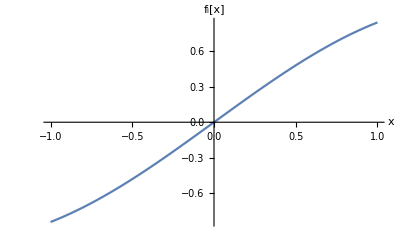

```mathematica
Plot[Sin[x],{x,-1,1},AxesLabel->{x,"\!\(\*SubscriptBox[\(f\), \(i\)]\)[x]"}]
```

```mathematica
Plot[f,{x,-1,1},AxesLabel->{x,Style[Row[{Subscript["f","i"],"(x)"}],FontFamily->"Times",12,Italic]}]
```

-Graphics-

```mathematica
Subscript["T","r"]
```

T_r

```mathematica
Row[{Subscript["T","r"], "/"3}]
```

T_r3 /

```mathematica
t==Subscript[T,r]-1
```

True

```mathematica
Clear[t]
```

```mathematica
num = 15;
omega = 2 * Sin[Range[num]*Pi/2/(num+1)];
alpha =Take[omega,{1,num-1}]/omega[[num]];
Q = 10^35;
A = Table[0,{i, 1,  num},{j,1,num}];
A[[1, 1]] = 1; 
For[i=1,i ≤num-1,i++, A[[1,i+1]]=
Round[Q*alpha[[i]]];];
For[i=2, i≤num, i++, A[[i,i]] = Q; ];
bb = LatticeReduce[A];
q = Abs[bb[[1,1]]]
error = Abs[N[q*alpha - Round[q* alpha],200]];
```

84350294911456044599486768675168